This notebook finds parameters to best fit the theoretical model of a DC motor to collected data.

Define constants

```mathematica
(* The maximum voltage of the motor. *)
motorVoltage=24;
```

```mathematica
(* The radius of the timing pulley on the axle of the motor in m. Multiplying angle change by this value gives the distance the cart moves. *)
timingPulleyRadius=0.00965;
```

Import the data

```mathematica
dataDirectory=FileNameJoin[{NotebookDirectory[],"..","data"}];
```

```mathematica
dataPaths=FileNames["*.csv",dataDirectory];
```

```mathematica
(* The columns are index, time (in ns), and angle (in degrees) *)
data=Import[#,"csv"]&/@dataPaths;
```

Calculate the PWM duty cycles and voltages from the file names

```mathematica
dataFilenames=FileNameSplit[#][[-1]]&/@dataPaths;
```

```mathematica
(* Moving to the left is considered positive *)
```

```mathematica
pwms=If[StringPart[#,1]=="l",1,-1]FromDigits[StringJoin[StringPart[#,{2,3}]]]&/@dataFilenames;
```

```mathematica
voltages=N[(# /255)motorVoltage]&/@pwms;
```

Drop the index column, convert time to seconds, add voltage, and convert angle to cart position

```mathematica
(* Time (in s), voltage (in V), position (in m) *)
positions=MapIndexed[
Module[
{voltage=voltages[[#2[[1]]]]},
{N[#[[2]]/1*^6],voltage,timingPulleyRadius#[[3]]Degree}&/@#1
]&,
data
];
```

Calculate velocities

```mathematica
(* Time (in s), voltage (in V), velocity (in m/s) *)
velocities={#[[2,1]],#[[2,2]],(#[[2,3]]-#[[1,3]])/(#[[2,1]]-#[[1,1]])}&/@Partition[#,2,1]&/@positions;
```

The time-dependent equation for the cart’s velocity has the form   where  and  are constants,  is the input voltage, and  is time. Find the parameters that best fit our data.

```mathematica
parameters=FindFit[Join@@velocities,a v(1-E^(-b t)),{a,b},{t,v}];
```

The time-independent equation for the cart’s acceleration has the form  where  and  are constants,  is the input voltage, and  is the cart’s velocity. Differentiating the time-dependent equation for the cart’s velocity above gives . Equating this with the time independent equation gives  or . From this we can see that  or  and   or .

```mathematica
c=a b/.parameters;
```

```mathematica
d=-b/.parameters;
```

Using these constants we can “integrate” the time-independent equation for the cart’s acceleration to get its velocity and plot this with the collected data.

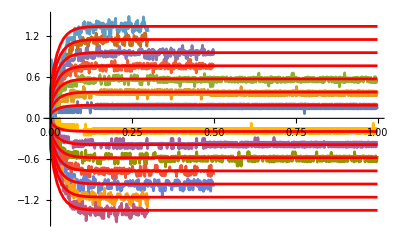

```mathematica
plot=GraphicsColumn[{
Text[c Subscript[V, in]+d v],
Show[
ListLinePlot[{#[[1]],#[[3]]}&/@#&/@velocities],
ListLinePlot[
Module[
{dt=0.01,voltage=#},
FoldList[{#2,#1[[2]]+(c voltage+d#1[[2]])dt}&,{0,0},Range[0,1,dt]]
]&/@voltages,
PlotStyle->Red
]]
}]
```

Uncomment to export an image of the plot

```mathematica
(*Export[
FileNameJoin[{NotebookDirectory[],"motor.png"}],
plot
];*)
```